```mathematica
BQA=1+0.1 Cos[θ];
BQH=1+0.1Cos[θ-4 ϕ];
BQI=(1+0.1 Cos[ϕ])(1+0.01 Sin[ϕ]Cos[θ-(-π/2+(ϕ-π)0.9)]);
```

```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"Latin Modern Math"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```

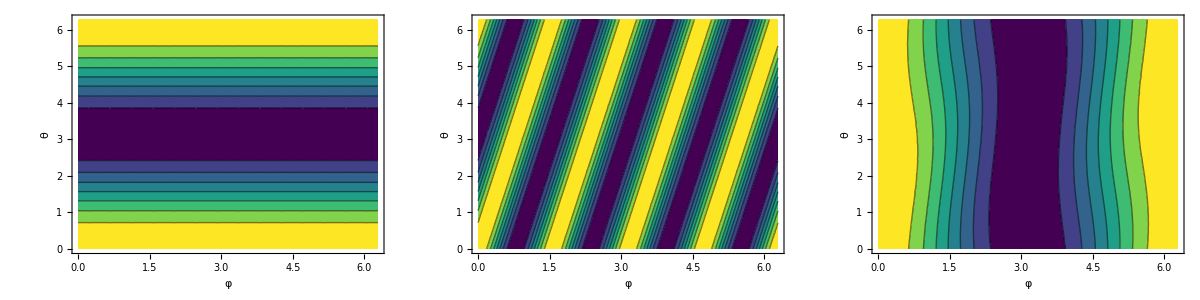

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
gridplot=Grid[{{
ContourPlot[BQA,{ϕ,0,2π},{θ,0,2π},ColorFunction->MPLColorMap["Viridis"],Contours->7,FrameLabel->{"φ","θ"}],
ContourPlot[BQH,{ϕ,0,2π},{θ,0,2π},ColorFunction->MPLColorMap["Viridis"],Contours->7,FrameLabel->{"φ","θ"}],
ContourPlot[BQI,{ϕ,0,2π},{θ,0,2π},ColorFunction->MPLColorMap["Viridis"],Contours->7,FrameLabel->{"φ","θ"}]}}]
```

```mathematica
Export["/Users/rogeriojorge/local/NearAxis_Optimization/Figures/QA_QI_QH.pdf",gridplot,ImageResolution->600]
```

/Users/rogeriojorge/local/NearAxis_Optimization/Figures/QA_QI_QH.pdf